```mathematica
(* Import data from Johns Hopkins *)
HopkinsConfirmed = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_confirmed_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsRecovered = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_recovered_global.csv",CharacterEncoding->"UTF8"],1];
HopkinsDeaths = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_deaths_global.csv",CharacterEncoding->"UTF8"],1];
CountryListOri=AlphabeticSort[DeleteDuplicates[Transpose[HopkinsConfirmed][[2]]]];
(*Export[NotebookDirectory[]<>"/countries.xls",TableForm[Table[{i,CountryListOri[[i]][[2]]},{i,1,Length[CountryList]}]],"XLS"];*)

(* Add population data and ISO code to the countrylist *)
ISOCountries =Drop[Import[NotebookDirectory[]<>"/ISO-countries.csv", CharacterEncoding->"UTF8"],1];
CountryList={};
For[i=1,i≤Length[CountryListOri],i++,
notfound=1;
For[j=1,j≤Length[ISOCountries],j++,
If[CountryListOri[[i]]==ISOCountries[[j]][[2]],notfound=0;CountryList=Append[CountryList,ISOCountries[[j]]]]
]
If[notfound==1,Print["Not found: "<>CountryListOri[[i]]]];
]
```

Not found: Diamond Princess

Not found: Kosovo

Not found: MS Zaandam

```mathematica
(* Data for countries can be split over multiple rows in the data from Hopkins *)
DataByCountry = Table[{},{i,1,Length[CountryList]}];
NumberOfDays = Length[Transpose[HopkinsConfirmed]]-4;

For[country = 1, country ≤ Length[CountryList],country++,
TempConfirmed=Table[0,{i,1,NumberOfDays}];
TempRecovered = Table[0,{i,1,NumberOfDays}];
TempDeaths = Table[0,{i,1,NumberOfDays}];
For[row=1,row≤ Length[HopkinsConfirmed],row++,
If[StringMatchQ[CountryList[[country]][[2]], HopkinsConfirmed[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempConfirmed = TempConfirmed + Drop[HopkinsConfirmed[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsRecovered],row++,
If[StringMatchQ[CountryList[[country]][[2]], HopkinsRecovered[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempRecovered= TempRecovered + Drop[HopkinsRecovered[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsDeaths],row++,
If[StringMatchQ[CountryList[[country]][[2]], HopkinsDeaths[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempDeaths = TempDeaths + Drop[HopkinsDeaths[[row]],4];
]
];
TempConfirmedDiff=TempConfirmed-Drop[Join[{0},TempConfirmed],-1];
TempRecoveredDiff=TempRecovered-Drop[Join[{0},TempRecovered],-1];
TempDeathsDiff=TempDeaths-Drop[Join[{0},TempDeaths],-1];
DataByCountry[[country]]= {ToString[CountryList[[country]][[2]]],TempConfirmed,TempRecovered,TempDeaths,TempConfirmedDiff,TempRecoveredDiff,TempDeathsDiff};
]
```

```mathematica
(* Model *)
SIR[country_,dday_] := (
n=n0;
e=e0;
i=i0;
r=0;
m=0;
c=r+r+m;
s = n-i-r-m;
cost = 0;
For[sirday=1,sirday≤ dday, sirday++,
lambda = (gamma+delta) * listr0[[sirday]][[2]];
ds = -lambda i *(s/n);
de=lambda i * (s/n)-epsilon e;
di = epsilon e -gamma i - delta i;
inew = lambda i * (s/n);
dr = gamma i;
dm = delta i;
dc=di +dr+dm;
s+=ds;
e+=de;
i+=di;
r+=dr;
m+=dm;
c+=dc;
n=s+e+i+r;
If[sirday≤ Length[DataByCountry[[country]][[2]]],
cost = cost + (c-DataByCountry[[country]][[2]][[sirday]])^2;];
];
Return[{s,i,r,m,c,cost,di,dm,inew}];
);
```

```mathematica
(* Initial values for this country *)
Window =4;(* Number of days over which to fit the model *)
future=30; (* Number of days to project ahead *)
```

```mathematica
CountrySIR[country_] := (
CurrentCountry =country;
today = Length[DataByCountry[[CurrentCountry]][[2]]];
CFR=DataByCountry[[CurrentCountry]][[4]][[-1]]/DataByCountry[[CurrentCountry]][[2]][[-1]];

n0 = CountryList[[country]][[3]];
e0=500;
i0=100;
epsilon = 1/2;
gamma=(1-CFR)/12.4;
delta = CFR/10.4;
listr0 = {};
For[day = 1, day <= Length[DataByCountry[[CurrentCountry]][[2]]] + future, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];

(* Fit model to the data *)
For[day=1,day≤Length[DataByCountry[[CurrentCountry]][[2]]]-Window,day++,
bestr0=listr0[[day]][[2]];
bestcost=SIR[CurrentCountry,day+Window][[6]];
For[kr0 = 0.05,kr0≤20,kr0=kr0+0.05,
(* set this possible r0 for all following days and see what the cost is *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] = kr0;];
temp=SIR[CurrentCountry,day + Window];
If[temp[[6]]<bestcost,bestcost=temp[[6]];bestr0=kr0;];
];

(* We found a good r0 for this day, set it for all the following days *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] =bestr0;];
];

(* Generate the lists of data for the plots *)
lists={};
listi={};
listr={};
listm={};
listc={};
listdi={};
listdm={};
listinew = {};
For[day=1,day≤Length[DataByCountry[[CurrentCountry]][[2]]]+future,day++,
temp=SIR[CurrentCountry,day];
lists=Append[lists,{day,temp[[1]]}];
listi=Append[listi,{day,temp[[2]]}];
listr=Append[listr,{day,temp[[3]]}];
listm=Append[listm,{day,temp[[4]]}];
listc=Append[listc,{day,temp[[5]]}];
listdi=Append[listdi,{day,temp[[7]]}];
listdm=Append[listdm,{day,temp[[8]]}];
listinew = Append[listinew,{day,temp[[9]]}];
];
Return[{CurrentCountry,DataByCountry[[CurrentCountry]][[1]],listr0,listi,listr,listm,listc,listdi,listdm,listinew}];
);
```

```mathematica
CountrySIR[17];
```

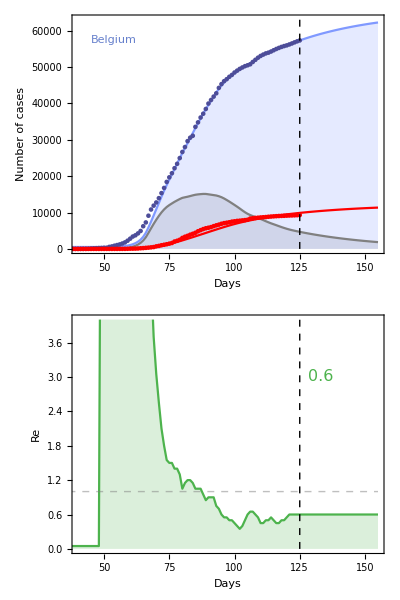

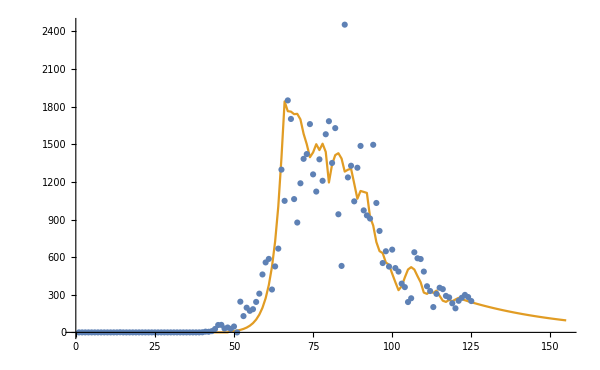

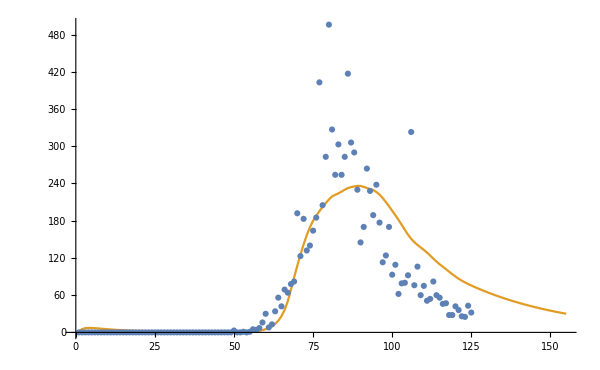

```mathematica
(* Generate plots *)
height=Max[ {Max[Drop[listc,-55]],Max[DataByCountry[[CurrentCountry]][[2]]]}];

If[listr0[[-1]][[2]]<0.8,R0Color=RGBColor[0.3,0.7,0.3],If[listr0[[-1]][[2]]>1.2,R0Color=RGBColor[0.7,0.3,0.3],R0Color=RGBColor[0.9,0.7,0.3]]];

plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], FontSize->16,R0Color],{today+3,3},{Left,Center}]}];

plotLine = Graphics[Style[Line[{{0, 1}, {today+future, 1}}],Dashed,RGBColor [0.5,0.5,0.5,0.5]]];

plotCountryname = Graphics[{Text[Style[DataByCountry[[CurrentCountry]][[1]], Large,RGBColor[0.4,0.5,0.8]],{45,1.00height},{Left,Center}]}];

plotModel=Show[{ListPlot[{listi,listc,DataByCountry[[CurrentCountry]][[2]],DataByCountry[[CurrentCountry]][[4]],listm},PlotRange->{{40,today+future},{0,1.10height}},Joined->{True,True,False,False,True},Filling->{1-> Bottom,2->Bottom},PlotStyle->{Gray,RGBColor[0.5,0.6,1],RGBColor[0.3,0.3,0.6],Red,Red},FrameLabel->{"Days","Number of cases"},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thickness[0.002],13],AspectRatio->1/1,ImageSize->600],plotCountryname}];

plotR0=ListPlot[listr0,Joined->True,Filling->{1->Bottom},PlotStyle->R0Color,FrameLabel->{"Days","Re"},FrameStyle->Directive[Thickness[0.002],13],Frame->True,FrameTicks->Automatic,AspectRatio->1/4,PlotRange->{{40,today+future},{0,4}},ImageSize->600];

ThePlotThickens=Multicolumn[{Show[{plotModel,Graphics[{Dashed, Line[{{today, 0}, {today, 1.2 height}}]}]},ImagePadding->{{70,10},{20,10}}],Show[{plotR0,plotFinalR0,plotLine,Graphics[{Dashed, Line[{{today, 0}, {today, 20}}]}]},ImagePadding->{{70,10},{40,5}}]},1]
CountryFilename=NotebookDirectory[]<>"/results/SIR-" <> ToString[DataByCountry[[CurrentCountry]][[1]]] <> "-" <> DateString[{"ISODate"}] <> ".pdf";
Export[CountryFilename, ThePlotThickens, ImageResolution -> 600];
ListPlot[{DataByCountry[[17]][[5]],listinew},Joined->{False,True},PlotRange->All,ImageSize->600]
ListPlot[{DataByCountry[[17]][[7]],listdm},Joined->{False,True},PlotRange->All,ImageSize->600]
```

```mathematica
R0PerCountry={};
For[country=1,country≤Length[CountryList],country++,
R0PerCountry = Append[R0PerCountry,CountrySIR[country]];
Print["Country: "<>R0PerCountry[[-1]][[2]]<>" -> "<>ToString[R0PerCountry[[-1]][[3]][[-1]][[2]]]];
]
```

Country: Afghanistan -> 1.8

Country: Albania -> 0.8

```mathematica
countryPlotted = {};
For[country=1,country≤Length[CountryList],country++,
MathematicaCountry=Entity["Country",StringReplace[ToString[CountryList[[country]][[2]]]," " -> ""]];
countryPlotted=Append[countryPlotted,MathematicaCountry->R0PerCountry[[country]][[3]][[-1]][[2]]];
];
```

```mathematica
WorldMap = GeoRegionValuePlot[countryPlotted,ImageSize->Large,ColorFunction->Function[{z},ColorData["TemperatureMap"][z/2]],ColorFunctionScaling->False,ImageSize->Full]
```

-Graphics-

```mathematica
WorldMapFilename=NotebookDirectory[]<>"/results/SIR-World-map-" <> DateString[{"ISODate"}] <> ".png";
Export[WorldMapFilename, WorldMap, ImageResolution -> 600];
```

```mathematica
(* Export CSV files for visualising online *)
(* Data for world map *)
ExportR0 = Table[{i,R0PerCountry[[i]][[2]],R0PerCountry[[i]][[3]][[-(future+1)]][[2]]},{i,1,Length[R0PerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-r0.csv",ExportR0];
ExportInfected = Table[{i,R0PerCountry[[i]][[2]],R0PerCountry[[i]][[4]][[-(future+1)]][[2]]},{i,1,Length[R0PerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-active.csv",ExportInfected];
ExportRecovered = Table[{i,R0PerCountry[[i]][[2]],R0PerCountry[[i]][[5]][[-(future+1)]][[2]]},{i,1,Length[R0PerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-recovered.csv",ExportRecovered];
ExportDeaths = Table[{i,R0PerCountry[[i]][[2]],R0PerCountry[[i]][[6]][[-(future+1)]][[2]]},{i,1,Length[R0PerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-deaths.csv",ExportDeaths];
ExportCumulative = Table[{i,R0PerCountry[[i]][[2]],R0PerCountry[[i]][[7]][[-(future+1)]][[2]]},{i,1,Length[R0PerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-cumulative.csv",ExportCumulative];
ExportActiveDiff = Table[{i,R0PerCountry[[i]][[2]],R0PerCountry[[i]][[8]][[-(future+1)]][[2]]},{i,1,Length[R0PerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-active-diff.csv",ExportActiveDiff];
ExportDeathsDiff = Table[{i,R0PerCountry[[i]][[2]],R0PerCountry[[i]][[9]][[-(future+1)]][[2]]},{i,1,Length[R0PerCountry]}];
Export[NotebookDirectory[]<>"results/csv/world-deaths-diff.csv",ExportDeathsDiff];


(* Data per country *)
ExportList={};
For [country=1,country≤ Length[R0PerCountry],country++,
ExportList=Append[ExportList,{R0PerCountry[[country]][[1]],R0PerCountry[[country]][[2]]}]
]
(* Name and ID *)
Export[NotebookDirectory[]<>"results/csv/country-general.csv",ExportList];
(* Calculated data, one file per data series per country *)
ExportList={};
For [country=1,country≤ Length[R0PerCountry],country++,
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-r0.csv",R0PerCountry[[country]][[3]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-i.csv",R0PerCountry[[country]][[4]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-r.csv",R0PerCountry[[country]][[5]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-m.csv",R0PerCountry[[country]][[6]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-c.csv",R0PerCountry[[country]][[7]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-di.csv",R0PerCountry[[country]][[8]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-dm.csv",R0PerCountry[[country]][[9]]];
]
(* Data from Johns Hopkins, one file per data series per country *)
For [country=1,country≤ Length[R0PerCountry],country++,
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-confirmed.csv",DataByCountry[[country]][[2]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-recovered.csv",DataByCountry[[country]][[3]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-deaths.csv",DataByCountry[[country]][[4]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-confirmed-diff.csv",DataByCountry[[country]][[5]]];
Export[NotebookDirectory[]<>"results/csv/country-"<>ToString[country]<>"-jh-recovered-diff.csv",DataByCountry[[country]][[6]]];
]
```